# Лабораторная работа №3

## Воинов Владислав, группа 421701, вариант 9

## 1.Отделить корни графически и найти один нецелый корень методом хорд при ε=10⁻.b3. Указать число итераций. Показать первые две хорды

### а) Графическое отделение корней

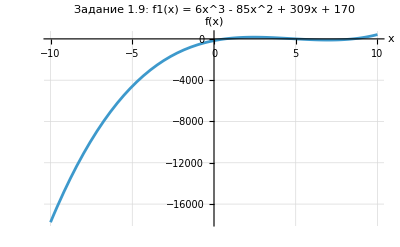

{{0.5,1.}}

```mathematica
ClearAll[f1,x];f1[x_]:=6 x^3-85 x^2+309 x-170;

Plot[f1[x],{x,-10,10},
PlotLabel->"Задание 1.9: f1(x) = 6x^3 - 85x^2 + 309x + 170",
AxesLabel->{"x","f(x)"},GridLines->Automatic]

(*Авто-поиск интервалов смены знака*)
signIntervals=
Module[{pts=Table[{ξ,f1[ξ]},{ξ,-10,10,0.5}]},
Select[Partition[pts,2,1],#[[1,2]] #[[2,2]]<0&][[All,All,1]]];
signIntervals  (*выбери любой интервал {a,b}*)
```

### б) Метод хорд (регула фальси) + вывод итераций

```mathematica
ClearAll[f1,x,eps];
f1[x_]:=6 x^3-85x^2+309x-170;
eps=10.^-3;

(*Гарантированный интервал со сменой знака*)
a1=0.5;b1=0.8;
fa=f1[a1];fb=f1[b1];

If[fa*fb>0,Print["[Хорды] Ошибка: на (-1,0) нет смены знака. Проверь f1."],Module[{a=a1,b=b1,fa=fa,fb=fb,c,fc,it=0,maxIter=200},While[it<maxIter,c=(a*fb-b*fa)/(fb-fa);
fc=f1[c];
If[Abs[fc]<eps||Abs[b-a]<eps,Break[]];
If[fa*fc<0,b=c;fb=fc,a=c;fa=fc];
it++;];
Print["[Хорды] корень ≈ ",NumberForm[N@c,{10,6}],", |f| = ",NumberForm[N@Abs@fc,{10,6}],", итераций = ",it+1];
c  (* <-оставить последней строкой,чтобы Out появился*)]]
```

[Хорды] корень ≈ 0.666668, |f| = 0.000300, итераций = 4

0.666668

### в) Иллюстрация первых двух хорд

c1 ≈ 0.425000, f(c1) ≈ -53.567531   |   c2 ≈ 0.620531, f(c2) ≈ -9.552188

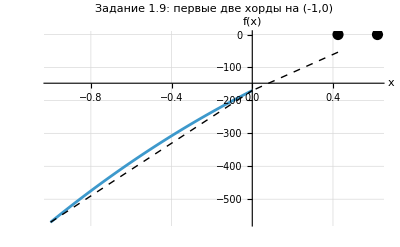

```mathematica
(*Интервал (-1,0) и две итерации вручную*)a=-1.;b=0.;
fa=f1[a];fb=f1[b];

(*1-я хорда*)
c1=(a*fb-b*fa)/(fb-fa);
fc1=f1[c1];

(*Обновляем отрезок*)
If[fa*fc1<0,b=c1;fb=fc1,a=c1;fa=fc1];

(*2-я хорда*)
c2=(a*fb-b*fa)/(fb-fa);
fc2=f1[c2];

(*Базовый график на исходном отрезке*)
gBase=Plot[f1[z],{z,-1,0},PlotLabel->"Задание 1.9: первые две хорды на (-1,0)",AxesLabel->{"x","f(x)"},GridLines->Automatic];

(*Линии-хорды и метки проекций на ось x*)
gChord1=Graphics[{Thick,Dashed,Line[{{-1,f1[-1]},{0,f1[0]}}],PointSize[0.02],Point[{c1,0}]}];

(*Для второй хорды используем обновлённый[a,b] после первого шага*)
gChord2=Graphics[{Thick,Dashed,Line[{{a,f1[a]},{b,f1[b]}}],PointSize[0.02],Point[{c2,0}]}];

Print["c1 ≈ ",NumberForm[N@c1,{10,6}],", f(c1) ≈ ",NumberForm[N@fc1,{10,6}],"   |   c2 ≈ ",NumberForm[N@c2,{10,6}],", f(c2) ≈ ",NumberForm[N@fc2,{10,6}]];

Show[gBase,gChord1,gChord2,PlotRange->All]
```

## Задание 2. Многочлен 6-й степени (вариант 2.9): графика, Solve, NSolve, Roots, FindRoot, Factor

### а) Графическое отделение

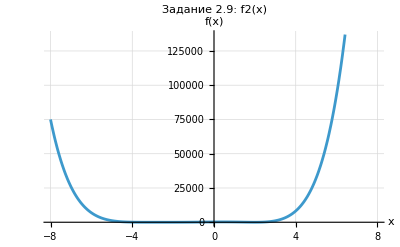

```mathematica
ClearAll[f2,x];f2[x_]:=x^6+7 x^5+5 x^4-55 x^3-90 x^2+108 x+216;

Plot[f2[x],{x,-8,8},
PlotLabel->"Задание 2.9: f2(x)",
AxesLabel->{"x","f(x)"},GridLines->Automatic]
```

### б) Solve, NSolve, Roots

```mathematica
solSolve=Quiet@Solve[f2[x]==0,x];
solNSolve=Quiet@NSolve[f2[x]==0,x,Reals];
solRoots=Quiet@Roots[f2[x]==0,x];

Print["Solve: ",solSolve];
Print["NSolve: ",solNSolve];
Print["Roots: ",solRoots];
```

Solve: {{x→-3},{x→-3},{x→-3},{x→-2},{x→2},{x→2}}

NSolve: {{x→-3.},{x→-3.},{x→-3.},{x→-2.},{x→2.},{x→2.}}

Roots: x==-3||x==-3||x==-3||x==-2||x==2||x==2

### в) Factor (разложение)

```mathematica
Print["Factor: ",Factor[f2[x]]];
```

Factor: (-2+x)^2 (2+x) (3+x)^3

### г) FindRoot из разных стартов (проверка)

```mathematica
starts=Range[-6,6,1];
fr=Table[Quiet@Check[FindRoot[f2[x]==0,{x,s}],$Failed],{s,starts}];
fr//Column
```

```mathematica
{{{x->-3.0000066855748866}}, {{x->-3.0000235101578863}}, {{x->-3.}}, {{x->-2.}}, {{x->-2.0000000000000013}}, {{x->-2.}}, {{x->2.0000000224560117}}, {{x->2.}}, {{x->2.000000029539738}}, {{x->2.0000000262321134}}, {{x->2.000000027624644}}, {{x->2.0000000281849304}}}
```

## Задание 3. Трансцендентное уравнение (вариант 3.9)

#### а) Графика + метод Ньютона (число итераций)

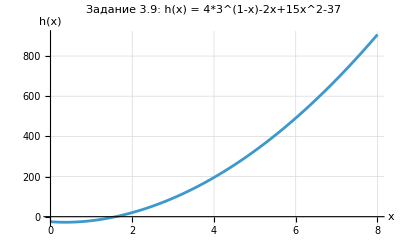

[Ньютон] корень ≈ 1.59383, итераций = 4

```mathematica
ClearAll[h,x];h[x_]:=4*3^(1-x)-2x+15x^2-37;

Plot[h[x],{x,10^-3,8},PlotLabel->"Задание 3.9: h(x) = 4*3^(1-x)-2x+15x^2-37",
AxesLabel->{"x","h(x)"},GridLines->Automatic]

newton[f_,x0_,eps_:1.*^-3,maxIter_:100]:=Module[
{x=x0,it=0,tr={x}},
While[it<maxIter,x=x-f[x]/(D[f[ξ],ξ]/. ξ->x);
AppendTo[tr,x];
If[Abs[f[x]]<eps,Return[<|"root"->x,"iters"->it+1,"trace"->tr|>]];
it++;];
<|"root"->x,"iters"->it,"trace"->tr,"note"->"maxIter"|>];

resN=newton[h,1.0,10.^-3];
Print["[Ньютон] корень ≈ ",N@resN["root"],", итераций = ",resN["iters"]];
```

### б) Метод секущих (число итераций)

```mathematica
secant[f_,x0_,x1_,eps_:1.*^-3,maxIter_:100]:=Module[
{a=x0,b=x1,fa=f[x0],fb=f[x1],c,fc,it=0,tr={x0,x1}},
While[it<maxIter,
c=b-fb (b-a)/(fb-fa);fc=f[c];AppendTo[tr,c];
If[Abs[fc]<eps,Return[<|"root"->c,"iters"->it+1,"trace"->tr|>]];
a=b;fa=fb;b=c;fb=fc;it++;
];
<|"root"->c,"iters"->it,"trace"->tr,"note"->"maxIter"|>
];

resS=secant[h,0.5,2.0,10.^-3];
Print["[Секущие] корень ≈ ",N@resS["root"],", итераций = ",resS["iters"]];
```

[Секущие] корень ≈ 1.59383, итераций = 5

## Задание 4. Привести (3.9) к виду x=g(x) и решить методом простых итераций

#### а) Построение g(x) (релаксация) и проверка |g’(x)|<1

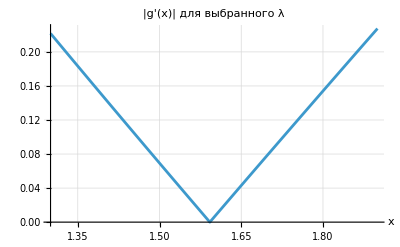

```mathematica
ClearAll[g,x,lam];
h[x_]:=4*3^(1-x)-2x+15x^2-37;

lam=0.023;               
g[x_]:=x-lam *h[x];

{A,B}={1.3,1.9};   
Plot[Abs[D[g[ξ],ξ]/. ξ->x],{x,A,B},
PlotLabel->"|g'(x)| для выбранного λ",AxesLabel->{"x",""},GridLines->Automatic]
```

#### б) Итерации x_{k+1}=g(x_k) (число итераций)

```mathematica
fixedPoint[g_,x0_,eps_:1.*^-3,maxIter_:200]:=Module[{x=x0,x1,it=0,tr={x0}},While[it<maxIter,x1=g[x];
If[!NumericQ[x1]||!FiniteQ[x1],Return[<|"note"->"overflow","iters"->it,"trace"->tr|>]];
AppendTo[tr,x1];
If[Abs[x1-x]<eps,Return[<|"root"->x1,"iters"->it+1,"trace"->tr|>]];
x=x1;it++;];
<|"note"->"maxIter","iters"->it,"trace"->tr|>];


resPI=fixedPoint[g,(A+B)/2,10.^-3];
Print["[Простые итерации] корень ≈ ",N@resPI["root"],", итераций = ",resPI["iters"]];
```

[Простые итерации] корень ≈ 1.59383, итераций = 2

## Задание 5. Решить уравнение (3.9) встроенными средствами: Solve, NSolve, FindRoot

#### а) Символьные/численные решения

```mathematica
ClearAll[x];h[x_]:=4*3^(1-x)-2x+15x^2-37;

Print["Solve: ",Quiet@N@Solve[h[x]==0,x]];
Print["NSolve: ",Quiet@NSolve[h[x]==0,x,Reals]];
Print["FindRoot: ",Quiet@FindRoot[h[x]==0,{x,1.0}]];
```

Solve: Solve[-37.+4. 3.^(1.-1. x)-2. x+15. x^2==0.,x]

NSolve: {{x→-0.744638},{x→1.59383}}

FindRoot: {x→1.59383}

## Задание 6. Система (вариант 6.9): на одном графике f=0, g=0, затем решить систему

#### а) График нулевых уровней f=0, g=0

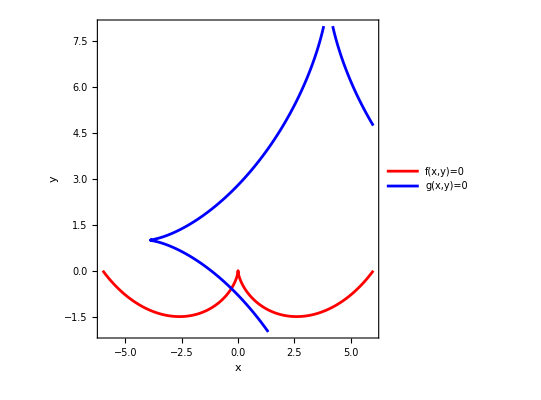

```mathematica
ClearAll[f6,g6,x,y];
f6[x_,y_]:=(x^2+y^2-6y)^2-36(x^2+y^2);
g6[x_,y_]:=Surd[(x-4)^2,3]+Surd[(y-1)^2,3]-4;

{xMin,xMax}={-6,6};{yMin,yMax}={-2,8}; 

ContourPlot[{f6[x,y]==0,g6[x,y]==0},
{x,xMin,xMax},{y,yMin,yMax},
ContourStyle->{Red,Blue},
PlotLegends->{"f(x,y)=0","g(x,y)=0"},
FrameLabel->{"x","y"},PlotPoints->50,MaxRecursion->2]
```

#### б) Численное решение системы (FindRoot) из нескольких стартов

```mathematica
ClearAll[f6,g6,x,y];
f6[x_,y_]:=(x^2+y^2-6y)^2-36(x^2+y^2);
g6[x_,y_]:=Surd[(x-4)^2,3]+Surd[(y-1)^2,3]-4;

starts={{-3.,3.},{-2.,4.},{0.5,4.},{2.,5.},{4.,6.}};

(*Функция решения из одной стартовой точки*)
solveFrom[{sx_?NumericQ,sy_?NumericQ}]:=Check[Quiet@FindRoot[{f6[x,y]==0,g6[x,y]==0},{{x,sx},{y,sy}},Method->"Secant",MaxIterations->200],$Failed];

(*Запускаем по всем стартам—ИСПОЛЬЗУЕМ Map (/@),НЕ Table с {sx,sy}*)
roots6=solveFrom/@starts;

(*Покажем «как есть»*)
Column[roots6]
```

{x→-0.295848,y→-0.58146}
{x→-0.521527,y→-0.391145}
{x→-1.68422,y→0.340463}
{x→-5.0231,y→2.41109}
{x→-2.7713,y→1.02641}

#### в) Попытка NSolve (по возможности)

```mathematica
Quiet@NSolve[
{f6[x,y]==0,g6[x,y]==0,y>=yMin,y<=yMax,x<=xMax,x>=xMin},
{x,y},Reals]
```

{{x→-0.295848,y→-0.58146}}